```mathematica
SetDirectory[NotebookDirectory[]]
pblue=Lighter[Blue];
pyellow=Lighter[Yellow];
pred=Lighter[Red];
pgreen=Lighter[Green];
cf=Piecewise[{{Blend[{pred,pblue},(#+Pi)/(Pi/2)],#≤-Pi/2},{Blend[{pblue,pgreen},(#+Pi/2)/(Pi/2)],#≤0},{Blend[{pgreen,pyellow},(#)/(Pi/2)],#≤Pi/2},{Blend[{pyellow,pred},(#-Pi/2)/(Pi/2)],#≤Pi}}]&;
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]]
phase[l:{_?NumericQ..}]:=Module[{args=Arg[l]},args+Prepend[2Pi Accumulate@-IntegerPart@Differences[args/Pi],0]]
nmax=10;
getphase[sig_]:=Module[{asig,plst,S1,slst1,f1},
asig=Fourier[ReplacePart[InverseFourier[sig-Mean[sig]],Join[{{1}},{#}&/@(Floor[Length[sig]/2]+Range[Floor[Length[sig]/2]])]->0]];
plst=phase[asig];
S1[n_]:=Sum[Exp[-I*n*plst[[i]]], {i,1,Length[plst]}]/Length[plst];
slst1=Table[S1[n]/(I*n),{n,1,nmax}];
f1[θ_]:=θ+Evaluate[Sum[2*Re[slst1][[n]]*(Cos[n*θ]-1)-2*Im[slst1][[n]]*Sin[n*θ],{n,1,nmax}]];
f1/@plst]
```

/home/zack/Desktop/snakingoscillators

### Janus oscillators

#### Single trajectory runs

{10,1,10000.,1000.,0.1}

{1,0.529613,68.0153,0.635064}

-Graphics-

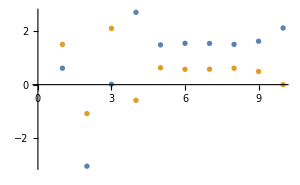
-Graphics- | -Graphics- | -Graphics- | -Graphics-

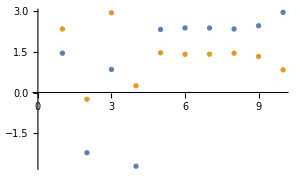
-Graphics- | -Graphics- | -Graphics- | -Graphics-

{68.0153,0.280489,18.4364}

```mathematica
filebase="data/chimeras/9";
dat=BinaryReadList[filebase<>"phases.npy","Real64"][[17;;-1]];
{M,seed,t1,t0,dt}=Import[filebase<>"out.dat"][[3]]
{seed,order,period,norm}=Import[filebase<>"out.dat"][[4]]
theta=ArcTan[Partition[dat,4*M][[All,1;;M]],Partition[dat,4*M][[All,M+1;;2*M]]];
phi=ArcTan[Partition[dat,4*M][[All,2*M+1;;3*M]],Partition[dat,4*M][[All,3*M+1;;4*M]]];
orders=BinaryReadList[filebase<>"order.npy","Real64"][[17;;-1]];
rasterizeBackground[ListPlot[orders,ImageSize->300,PlotRange->{0,1}]]
phases=Transpose[Catenate[{Transpose[theta],Transpose[phi]}]];
dphases=(Mod[#-#[[-1]]+Pi,2*Pi]-Pi&/@phases);

If[period>0,
nperiod=Round[period/dt];
Grid[{{rasterizeBackground[ListDensityPlot[dphases[[-nperiod;;-1,1;;M]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListDensityPlot[dphases[[-nperiod;;-1,M+1;;2*M]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListPlot[Transpose[{Cos[dphases[[All,2]]],Cos[dphases[[All,M+1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300]],ListPlot[{dphases[[-1,1;;M]],dphases[[-1,M+1;;-1]]},ImageSize->300]}}]]
If[period>0,
nperiod=Round[period/dt];
Grid[{{rasterizeBackground[ListDensityPlot[phases[[-nperiod;;-1,1;;M]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListDensityPlot[phases[[-nperiod;;-1,M+1;;2*M]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListPlot[Transpose[{Cos[phases[[All,2]]],Cos[phases[[All,M+1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300]],ListPlot[{phases[[-1,1;;M]],phases[[-1,M+1;;-1]]},ImageSize->300]}}]]
If[period>0,{period,Mean[orders[[-nperiod;;-1]]],Norm[Differences[dphases[[-nperiod+1;;-1]]],2]}]
```

```mathematica
Mean[Table[Abs[Sum[1/(2*M)*(Exp[I*theta[[n,i]]]+Exp[I*phi[[n,i]]]),{i,1,M}]]^2,{n,1,nperiod}]]^0.5
Mean[Table[Abs[Sum[1/(2*M)*(Exp[I*(theta[[n,i]]+2*Pi/M*(i-1))]+Exp[I*(phi[[n,i]]+2*Pi/M*(i-1))]),{i,1,M}]]^2,{n,1,nperiod}]]^0.5
Mean[Table[Abs[Sum[1/(2*M)*(Exp[I*(theta[[n,i]]-2*Pi/M*(i-1))]+Exp[I*(phi[[n,i]]-2*Pi/M*(i-1))]),{i,1,M}]]^2,{n,1,nperiod}]]^0.5
```

0.52962

0.258456

0.258456

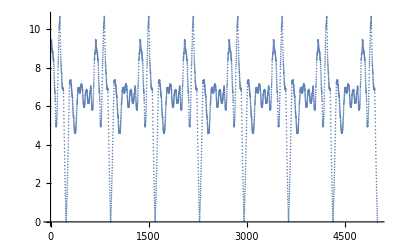

{68.0153}

```mathematica
norms=Norm[Mod[#-dphases[[-1]]+Pi,2*Pi]-Pi,2]&/@(dphases);
ListPlot[norms[[-5000;;-1]]]
mins=Position[Differences[Sign[Differences[norms]]],2];
Mean[Differences[Extract[mins,Position[Extract[norms,mins],u_/;u<1]]]]*dt
```

#### AUTO periodic ics

```mathematica
vals={#[[1]],#[[2]],#[[3]]/300,#[[4]]}&/@SortBy[Import["random.dat"],Norm[#[[2;;4]]]&];
dorder=0.01;
dperiod=0.01;
dnorm=0.01;
{bins,array}=HistogramList[vals[[All,2;;4]],{{dorder*(Range[1/dorder]-1)},{0.1+dperiod*(Range[3/dperiod]-1)},{dnorm*(Range[2/dnorm]-1)}}];
uniq=Table[{i,j,k}=case;
First@Cases[vals,u_/;u[[2]]>=bins[[1,i]]&&u[[2]]<=bins[[1,i+1]]&&u[[3]]>=bins[[2,j]]&&u[[3]]<=bins[[2,j+1]]&&u[[4]]>=bins[[3,k]]&&u[[4]]<=bins[[3,k+1]]],{case,(First/@ArrayRules[array])[[1;;-2]]}];
Length[uniq]
SortBy[{#[[1]],#[[2]],#[[3]]*300,#[[4]]}&/@uniq,{#[[2]],#[[3]],#[[4]]}&]

If[!DirectoryQ["data/chimeras"],CreateDirectory["data/chimeras"]]
seeds=uniq[[All,1]];
Do[CopyFile["data/random/"<>ToString[seeds[[i]]]<>"fs.npy","data/chimeras/"<>ToString[i]<>"ic.npy",OverwriteTarget->True], {i,1,Length[seeds]}]
Last/@ArrayRules[array][[1;;-2]]
```

10

{{800,0.357188,67.1923,1.45206},{37,0.43029,74.2333,0.872678},{811,0.494775,65.2571,0.050774},{680,0.494791,65.2571,0.0610488},{401,0.494792,65.2571,0.0282475},{485,0.494811,65.2571,9.58402×10^-17},{489,0.494981,65.2571,0.039411},{1002,0.514847,74.4833,0.235634},{132,0.52962,68.0154,0.634891},{385,0.700155,70.9538,0.141218}}

{4,1,11,9,12,12,13,4,71,177}

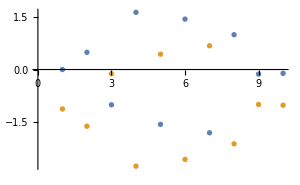
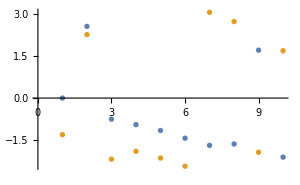
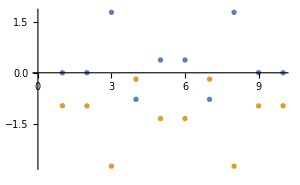
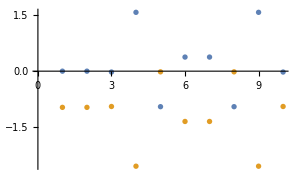
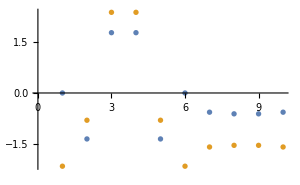
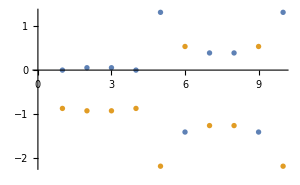
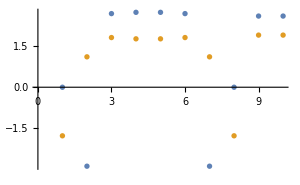
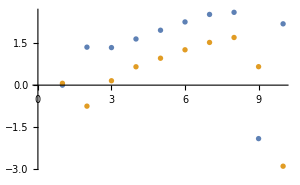
1 | 0.35716 | 67.1917 | 1.45181 | 3.72098 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
2 | 0.430291 | 74.2308 | 0.873108 | 12.5267 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
3 | 0.495039 | 65.2625 | 2.85671×10^-18 | 12.3915 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
4 | 0.495011 | 65.2618 | 0.0281866 | 12.4275 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
5 | 0.495106 | 65.2618 | 0.038832 | 15.8485 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
6 | 0.494981 | 65.2618 | 0.0507718 | 15.6571 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
7 | 0.495052 | 65.2618 | 0.0610565 | 15.6412 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
8 | 0.514878 | 74.4824 | 0.236264 | 5.40575 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
9 | 0.529613 | 68.0153 | 0.635064 | 5.43191 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
10 | 0.700107 | 70.9552 | 0.142189 | 10.8239 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Monitor[p=Grid[DeleteCases[Table[filebase="data/chimeras/"<>ToString[j];
{seed,order,period,norm}=Import[filebase<>"out.dat"][[-1]];
dat=BinaryReadList[filebase<>"phases.npy","Real64"][[17;;-1]];
M=10;
theta=ArcTan[Partition[dat,4*M][[All,1;;M]],Partition[dat,4*M][[All,M+1;;2*M]]];
phi=ArcTan[Partition[dat,4*M][[All,2*M+1;;3*M]],Partition[dat,4*M][[All,3*M+1;;4*M]]];
phases=Transpose[Catenate[{Transpose[theta],Transpose[phi]}]];
phases2=Transpose[Catenate[{-Reverse[Transpose[phi]],-Reverse[Transpose[theta]]}]];
dphases=(Mod[#-#[[1]]+Pi,2*Pi]-Pi&/@phases);
dphases2=(#-#[[1]]&/@phases2);
norms=Norm[Mod[#-dphases[[-1]]+Pi,2*Pi]-Pi]&/@dphases;
mins=First/@Position[Differences[Sign[Differences[norms]]],u_/;u>0];
periods=Differences[Cases[mins,u_/;norms[[u]]<1]];
test=Norm[Mod[dphases[[-Round[period/0.1];;-1]]-dphases[[-10*Round[period/0.1];;-9*Round[period/0.1]-1]]+Pi,2*Pi]-Pi];
If[period>0,
{Grid[{{j,order,period,norm,test,rasterizeBackground[ListDensityPlot[dphases[[1;;Round[period/0.1];;10,1;;M]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListDensityPlot[dphases[[1;;Round[period/0.1];;10,M+1;;2*M]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListPlot[Transpose[{Cos[dphases[[All,2]]],Cos[dphases[[All,M+1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300]],rasterizeBackground[ListPlot[Transpose[{Cos[dphases2[[All,2]]],Cos[dphases2[[All,M+1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300]],ListPlot[{dphases[[-1,1;;M]],dphases[[-1,M+1;;-1]]},ImageSize->300]}}]}],{j,1,Length[uniq]}],Null]],j]
```

#### AUTO steady ics

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{η→-2.36793},{η→-1.49156}}

{1:0.809017,2:0.309017,3:-0.309017,4:-0.809017,5:-1.0,6:-0.809017,7:-0.309017,8:0.309017,9:0.809017,10:0.587785,11:0.951057,12:0.951057,13:0.587785,14:0.0,15:-0.587785,16:-0.951057,17:-0.951057,18:-0.587785,19:-0.715353,20:-0.16801,21:0.443507,22:0.88562,23:0.989455,24:0.715353,25:0.16801,26:-0.443507,27:-0.88562,28:-0.989455,29:-0.698763,30:-0.985785,31:-0.896271,32:-0.464411,33:0.144838,34:0.698763,35:0.985785,36:0.896271,37:0.464411,38:-0.144838}

{-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2}

{0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2}

2.48253×10^-17

1.24127×10^-17

0.377258

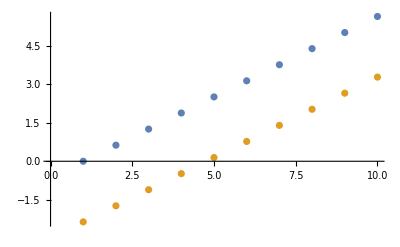

{1:0.809017,2:0.309017,3:-0.309017,4:-0.809017,5:-1.0,6:-0.809017,7:-0.309017,8:0.309017,9:0.809017,10:0.587785,11:0.951057,12:0.951057,13:0.587785,14:0.0,15:-0.587785,16:-0.951057,17:-0.951057,18:-0.587785,19:0.0791545,20:0.649978,21:0.972533,22:0.923612,23:0.521904,24:-0.0791545,25:-0.649978,26:-0.972533,27:-0.923612,28:-0.521904,29:-0.996862,30:-0.759953,31:-0.232767,32:0.383328,33:0.853004,34:0.996862,35:0.759953,36:0.232767,37:-0.383328,38:-0.853004}

{-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2}

{0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2}

2.22045×10^-17

3.14018×10^-17

0.734559

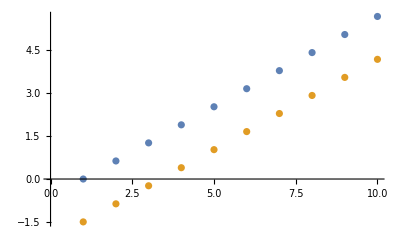

```mathematica
sols=Solve[0==1+2*0.25*Sin[η]+2*0.33*Sin[η+2*Pi/M],η]
thetas=Table[2*Pi/M*i,{i,1,M-1}];
phis=Table[η+2*Pi/M*i,{i,0,M-1}]/.sols[[1]];
u=Catenate[N[{Cos[thetas],Sin[thetas],Cos[phis],Sin[phis]}]];
Table[ToString[i]<>":"<>TextString[u[[i]]],{i,1,4*M-2}]

theta=N[Join[{0},thetas]];
Table[ω/2+β*Sin[phis[[i]]-theta[[i]]]+σ*Sin[phis[[Mod[i+1-1,M]+1]]-theta[[i]]],{i,1,M}]
Table[-ω/2+β*Sin[theta[[i]]-phis[[i]]]+σ*Sin[theta[[Mod[i-1-1,M]+1]]-phis[[i]]],{i,1,M}]
Abs[Total[Exp[I*theta]+Exp[I*phis]]/(2*M)]
Abs[Total[Exp[I*(theta+2*Pi*Range[M]/M)]+Exp[I*(phis+2*Pi*Range[M]/M)]]/(2*M)]
Abs[Total[Exp[I*(theta-2*Pi*Range[M]/M)]+Exp[I*(phis-2*Pi*Range[M]/M)]]/(2*M)]
ListPlot[{theta,phis}]

thetas=Table[2*Pi/M*i,{i,1,M-1}];
phis=Table[η+2*Pi/M*i,{i,0,M-1}]/.sols[[2]];
u=Catenate[N[{Cos[thetas],Sin[thetas],Cos[phis],Sin[phis]}]];
Table[ToString[i]<>":"<>TextString[u[[i]]],{i,1,4*M-2}]

theta=N[Join[{0},thetas]];
Table[ω/2+β*Sin[phis[[i]]-theta[[i]]]+σ*Sin[phis[[Mod[i+1-1,M]+1]]-theta[[i]]],{i,1,M}]
Table[-ω/2+β*Sin[theta[[i]]-phis[[i]]]+σ*Sin[theta[[Mod[i-1-1,M]+1]]-phis[[i]]],{i,1,M}]
Abs[Total[Exp[I*theta]+Exp[I*phis]]/(2*M)]
Abs[Total[Exp[I*(theta+2*Pi*Range[M]/M)]+Exp[I*(phis+2*Pi*Range[M]/M)]]/(2*M)]
Abs[Total[Exp[I*(theta-2*Pi*Range[M]/M)]+Exp[I*(phis-2*Pi*Range[M]/M)]]/(2*M)]
ListPlot[{theta,phis}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{η→-1.65003},{η→-0.773667}}

{1:0.809017,2:0.309017,3:-0.309017,4:-0.809017,5:-1.0,6:-0.809017,7:-0.309017,8:0.309017,9:0.809017,10:-0.587785,11:-0.951057,12:-0.951057,13:-0.587785,14:0.0,15:0.587785,16:0.951057,17:0.951057,18:0.587785,19:-0.0791545,20:-0.649978,21:-0.972533,22:-0.923612,23:-0.521904,24:0.0791545,25:0.649978,26:0.972533,27:0.923612,28:0.521904,29:-0.996862,30:-0.759953,31:-0.232767,32:0.383328,33:0.853004,34:0.996862,35:0.759953,36:0.232767,37:-0.383328,38:-0.853004}

{-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2,-0.996862 β-0.759953 σ+ω/2}

{0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2,0.996862 β+0.759953 σ-ω/2}

0.

0.678545

2.00148×10^-17

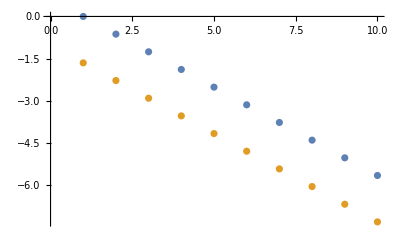

{1:0.809017,2:0.309017,3:-0.309017,4:-0.809017,5:-1.0,6:-0.809017,7:-0.309017,8:0.309017,9:0.809017,10:-0.587785,11:-0.951057,12:-0.951057,13:-0.587785,14:0.0,15:0.587785,16:0.951057,17:0.951057,18:0.587785,19:0.715353,20:0.16801,21:-0.443507,22:-0.88562,23:-0.989455,24:-0.715353,25:-0.16801,26:0.443507,27:0.88562,28:0.989455,29:-0.698763,30:-0.985785,31:-0.896271,32:-0.464411,33:0.144838,34:0.698763,35:0.985785,36:0.896271,37:0.464411,38:-0.144838}

{-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2,-0.698763 β-0.985785 σ+ω/2}

{0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2,0.698763 β+0.985785 σ-ω/2}

4.44089×10^-17

0.926108

4.00297×10^-17

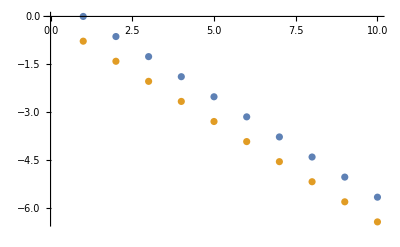

```mathematica
sols=Solve[0==1+2*0.25*Sin[η]+2*0.33*Sin[η-2*Pi/M],η]
thetas=Table[-2*Pi/M*i,{i,1,M-1}];
phis=Table[η-2*Pi/M*i,{i,0,M-1}]/.sols[[1]];
u=Catenate[N[{Cos[thetas],Sin[thetas],Cos[phis],Sin[phis]}]];
Table[ToString[i]<>":"<>TextString[u[[i]]],{i,1,4*M-2}]

theta=N[Join[{0},thetas]];
Table[ω/2+β*Sin[phis[[i]]-theta[[i]]]+σ*Sin[phis[[Mod[i+1-1,M]+1]]-theta[[i]]],{i,1,M}]
Table[-ω/2+β*Sin[theta[[i]]-phis[[i]]]+σ*Sin[theta[[Mod[i-1-1,M]+1]]-phis[[i]]],{i,1,M}]
Abs[Total[Exp[I*theta]+Exp[I*phis]]/(2*M)]
Abs[Total[Exp[I*(theta+2*Pi*Range[M]/M)]+Exp[I*(phis+2*Pi*Range[M]/M)]]/(2*M)]
Abs[Total[Exp[I*(theta-2*Pi*Range[M]/M)]+Exp[I*(phis-2*Pi*Range[M]/M)]]/(2*M)]
ListPlot[{theta,phis}]

thetas=Table[-2*Pi/M*i,{i,1,M-1}];
phis=Table[η-2*Pi/M*i,{i,0,M-1}]/.sols[[2]];
u=Catenate[N[{Cos[thetas],Sin[thetas],Cos[phis],Sin[phis]}]];
Table[ToString[i]<>":"<>TextString[u[[i]]],{i,1,4*M-2}]

theta=N[Join[{0},thetas]];
Table[ω/2+β*Sin[phis[[i]]-theta[[i]]]+σ*Sin[phis[[Mod[i+1-1,M]+1]]-theta[[i]]],{i,1,M}]
Table[-ω/2+β*Sin[theta[[i]]-phis[[i]]]+σ*Sin[theta[[Mod[i-1-1,M]+1]]-phis[[i]]],{i,1,M}]
Abs[Total[Exp[I*theta]+Exp[I*phis]]/(2*M)]
Abs[Total[Exp[I*(theta+2*Pi*Range[M]/M)]+Exp[I*(phis+2*Pi*Range[M]/M)]]/(2*M)]
Abs[Total[Exp[I*(theta-2*Pi*Range[M]/M)]+Exp[I*(phis-2*Pi*Range[M]/M)]]/(2*M)]
ListPlot[{theta,phis}]
```

```mathematica
η=0;
σ=0.33;
β=0.25;
ω=1;
θ1=0;
AbsoluteTiming[vals=Mod[{θ2,ϕ1,ϕ2},2*Pi]/.DeleteCases[Table[SeedRandom[seed];Quiet[Check[FindRoot[{0==ω/2+β*Sin[ϕ1]+σ*Sin[ϕ2+η],0==-ω/2+β*Sin[-ϕ1]+σ*Sin[θ2-ϕ1-η],0==ω/2+β*Sin[ϕ2-θ2]+σ*Sin[ϕ1-θ2+η]},{{θ2,2*Pi*RandomReal[]},{ϕ1,2*Pi*RandomReal[]},{ϕ2,2*Pi*RandomReal[]}}],{}]],{seed,1,10000}],{}];]
dtheta=0.01;
{bins,array}=HistogramList[vals[[All,1;;3]],{{-Pi*dtheta+2*Pi*dtheta*(Range[1.0/dtheta]-1)},{-Pi*dtheta+2*Pi*dtheta*(Range[1.0/dtheta]-1)},{-Pi*dtheta+2*Pi*dtheta*(Range[1.0/dtheta]-1)}}];
uniq=Table[{i,j,k}=case;
First@Cases[vals,u_/;u[[1]]>=bins[[1,i]]&&u[[1]]<=bins[[1,i+1]]&&u[[2]]>=bins[[2,j]]&&u[[2]]<=bins[[2,j+1]]&&u[[3]]>=bins[[3,k]]&&u[[3]]<=bins[[3,k+1]]],{case,(First/@ArrayRules[array])[[1;;-2]]}];
{Length[uniq],Length[vals]}
SortBy[{#[[1]],#[[2]],#[[3]]}&/@uniq,{#[[1]],#[[2]],#[[3]]}&]
```

{8.65469,Null}

{162,9891}

{{2.50843×10^-16,4.18093,4.18093},{8.88178×10^-16,5.24385,5.24385},{0.00123161,4.18163,5.24438},{0.00296332,5.24553,4.18221},{0.012194,4.1879,5.24907},{0.0274871,5.25933,4.19294},{0.0363825,5.26427,4.19689},{0.0695026,4.22149,5.27279},{0.0971908,4.23821,5.28376},{0.109267,4.24561,5.28844},{0.11871,5.30845,4.23504},{0.123738,5.31105,4.23746},{0.146243,5.32258,4.24844},{0.164472,4.28022,5.30903},{0.181865,4.2914,5.31524},{0.202555,4.30488,5.32245},{0.210921,5.35451,4.28119},{0.2386,5.36761,4.29577},{0.251174,5.37345,4.3025},{0.258018,5.3766,4.3062},{0.272012,4.35157,5.34522},{0.286775,4.36179,5.34976},{0.294723,4.36734,5.35217},{0.313969,5.40151,4.33724},{0.348936,5.41632,4.35739},{0.354966,4.4104,5.36934},{0.36902,5.42455,4.36925},{0.379407,4.42842,5.37577},{0.397839,4.44222,5.3804},{0.407359,5.43968,4.39246},{0.413709,4.45425,5.38423},{0.46271,5.4601,4.42739},{0.465839,4.49483,5.39578},{0.466353,5.46138,4.42975},{0.475146,4.50225,5.39767},{0.475383,5.46453,4.43563},{0.537287,4.55326,5.4088},{0.542926,5.48643,4.48128},{0.562092,4.57438,5.41249},{0.571584,5.49479,4.50157},{0.595874,5.5014,4.51925},{0.603203,5.50331,4.52467},{0.608366,4.61506,5.41808},{0.61618,4.6221,5.41885},{0.653315,5.51516,4.56293},{0.663702,4.66613,5.42235},{0.664287,5.51746,4.5716},{0.711119,4.7123,5.42359},{0.722441,5.52765,4.61957},{0.731553,4.73298,5.42335},{0.752077,5.53139,4.64547},{0.779868,4.78403,5.42061},{0.788148,5.53439,4.67853},{0.789947,4.79511,5.41962},{0.798148,5.53489,4.68804},{0.806663,4.81383,5.41761},{0.851564,5.53465,4.74169},{0.852473,4.86775,5.4095},{0.864781,5.53372,4.75584},{0.887129,4.91158,5.40033},{0.904859,4.93524,5.39439},{0.910477,5.52715,4.8081},{0.927751,4.9673,5.38523},{0.929414,5.52256,4.83163},{0.947388,4.99642,5.37575},{0.964503,5.02328,5.366},{0.971165,5.50709,4.88885},{0.983718,5.50053,4.90797},{0.984633,5.0571,5.35231},{0.998236,5.49144,4.93157},{1.00197,5.08872,5.33802},{1.02396,5.13364,5.3151},{1.02946,5.14606,5.30818},{1.03024,5.463,4.99202},{1.03213,5.46079,4.99612},{1.03703,5.1642,5.2976},{1.04034,5.45018,5.01493},{1.04829,5.19434,5.27873},{1.05262,5.42999,5.0474},{1.06316,5.24486,5.24308},{1.06573,5.39668,5.09382},{1.07109,5.37261,5.12325},{1.07311,5.30471,5.19318},{1.07376,5.31378,5.18476},{1.07402,5.31894,5.17986},{5.20911,4.08237,4.26834},{5.20969,4.11513,4.23615},{5.21224,4.05129,4.30255},{5.21504,4.15648,4.20015},{5.21811,4.02587,4.33383},{5.22045,4.18167,4.18037},{5.23038,3.99515,4.37682},{5.23357,4.22658,4.14858},{5.23993,4.24447,4.13705},{5.24374,3.97335,4.41198},{5.25116,4.27272,4.12003},{5.25136,3.96362,4.42933},{5.25271,3.96205,4.43225},{5.2644,4.30233,4.10367},{5.29251,3.92838,4.50572},{5.297,4.36496,4.07364},{5.30148,3.92312,4.51995},{5.30727,4.38266,4.0662},{5.31436,3.91658,4.53937},{5.32859,4.41723,4.05295},{5.33473,4.42674,4.04959},{5.35856,4.46196,4.03819},{5.36561,3.8992,4.60801},{5.37284,3.8976,4.61683},{5.37899,4.49043,4.03015},{5.38425,4.49754,4.0283},{5.3899,3.89448,4.63701},{5.43322,4.56008,4.01473},{5.43432,3.88999,4.68593},{5.46348,4.596,4.00907},{5.46849,3.88942,4.72066},{5.48379,4.61914,4.00624},{5.49554,3.89042,4.74672},{5.52919,4.66848,4.0023},{5.53499,3.89382,4.78276},{5.555,4.69524,4.00135},{5.56225,3.89735,4.80649},{5.58182,4.72217,4.00124},{5.60953,3.90544,4.84568},{5.61626,4.75559,4.00227},{5.63251,3.91019,4.86392},{5.64374,4.78138,4.00395},{5.6579,3.91598,4.88351},{5.67883,4.81331,4.00711},{5.68664,3.9232,4.90504},{5.70529,4.8367,4.01019},{5.71003,3.92955,4.92207},{5.72628,3.9342,4.93367},{5.74714,4.87256,4.01617},{5.75645,3.94333,4.95471},{5.78989,4.9079,4.02359},{5.81303,4.92651,4.02811},{5.8154,3.96289,4.9941},{5.85469,4.95918,4.0371},{5.85804,3.97835,5.02128},{5.87491,3.98475,5.03175},{5.89255,3.99161,5.04254},{5.90127,4.99449,4.04837},{5.91506,5.00472,4.05194},{5.93703,4.00961,5.06901},{5.93738,5.02105,4.05793},{5.94873,4.01452,5.07581},{5.97423,5.04744,4.06839},{5.99395,5.06127,4.07427},{6.01889,4.04531,5.11517},{6.03223,4.05143,5.12239},{6.04275,5.09471,4.08963},{6.04582,4.05774,5.12967},{6.06579,5.11011,4.09727},{6.09647,4.082,5.15606},{6.10189,5.13374,4.10974},{6.11899,5.14474,4.11585},{6.13421,4.10081,5.175},{6.15448,4.11116,5.18491},{6.17538,5.18007,4.1369},{6.18357,5.18509,4.14007},{6.1845,4.12681,5.19928}}

```mathematica
Monitor[Do[{θ2,ϕ1,ϕ2}=uniq[[i]];
thetas=Riffle[Table[θ2+η*i,{i,1,M-1,2}],Table[0+η*i,{i,2,M-1,2}]];
phis=Riffle[Table[ϕ1+η*i,{i,0,M-1,2}],Table[ϕ2+η*i,{i,1,M-1,2}]];
u=Catenate[N[{Cos[thetas],Sin[thetas],Cos[phis],Sin[phis]}]];
lines=StringJoin[{Import["auto/clusters/c.cluster"],"\nU="<>ToString[Table[ToString[i]<>":"<>TextString[u[[i]]],{i,1,4*M-2}]]}];
file=OpenWrite["auto/clusters/c.cluster"<>ToString[i]];
WriteLine[file,lines];
Close[file];,{i,1,Length[uniq]}],i]
```

```mathematica
η=2*Pi/M;
σ=0.33;
β=0.25;
ω=1;
θ1=0;
AbsoluteTiming[vals=Mod[{θ2,ϕ1,ϕ2},2*Pi]/.DeleteCases[Table[SeedRandom[seed];Quiet[Check[FindRoot[{0==ω/2+β*Sin[ϕ1]+σ*Sin[ϕ2+η],0==-ω/2+β*Sin[-ϕ1]+σ*Sin[θ2-ϕ1-η],0==ω/2+β*Sin[ϕ2-θ2]+σ*Sin[ϕ1-θ2+η]},{{θ2,2*Pi*RandomReal[]},{ϕ1,2*Pi*RandomReal[]},{ϕ2,2*Pi*RandomReal[]}}],{}]],{seed,1,10000}],{}];]
dtheta=0.01;
{bins,array}=HistogramList[vals[[All,1;;3]],{{-Pi*dtheta+2*Pi*dtheta*(Range[1.0/dtheta]-1)},{-Pi*dtheta+2*Pi*dtheta*(Range[1.0/dtheta]-1)},{-Pi*dtheta+2*Pi*dtheta*(Range[1.0/dtheta]-1)}}];
uniq=Table[{i,j,k}=case;
First@Cases[vals,u_/;u[[1]]>=bins[[1,i]]&&u[[1]]<=bins[[1,i+1]]&&u[[2]]>=bins[[2,j]]&&u[[2]]<=bins[[2,j+1]]&&u[[3]]>=bins[[3,k]]&&u[[3]]<=bins[[3,k+1]]],{case,(First/@ArrayRules[array])[[1;;-2]]}];
{Length[uniq],Length[vals]}
uniq
```

{9.1742,Null}

{6,9331}

{{-1.35285×10^-16,3.91526,3.91526},{6.86275×10^-16,4.79163,4.79163},{0.370635,5.08302,4.71239},{0.445814,4.08407,4.52988},{5.83737,4.08407,3.63826},{5.91255,4.34175,4.71239}}

```mathematica
Monitor[Do[{θ2,ϕ1,ϕ2}=uniq[[i]];
thetas=Riffle[Table[θ2+η*i,{i,1,M-1,2}],Table[0+η*i,{i,2,M-1,2}]];
phis=Riffle[Table[ϕ1+η*i,{i,0,M-1,2}],Table[ϕ2+η*i,{i,1,M-1,2}]];
u=Catenate[N[{Cos[thetas],Sin[thetas],Cos[phis],Sin[phis]}]];
lines=StringJoin[{Import["auto/clusters1/c.cluster"],"\nU="<>ToString[Table[ToString[i]<>":"<>TextString[u[[i]]],{i,1,4*M-2}]]}];
file=OpenWrite["auto/clusters1/c.cluster"<>ToString[i]];
WriteLine[file,lines];
Close[file];,{i,1,Length[uniq]}],i]
```

```mathematica
η=-2*Pi/M;
σ=0.33;
β=0.25;
ω=1;
θ1=0;
AbsoluteTiming[vals=Mod[{θ2,ϕ1,ϕ2},2*Pi]/.DeleteCases[Table[SeedRandom[seed];Quiet[Check[FindRoot[{0==ω/2+β*Sin[ϕ1]+σ*Sin[ϕ2+η],0==-ω/2+β*Sin[-ϕ1]+σ*Sin[θ2-ϕ1-η],0==ω/2+β*Sin[ϕ2-θ2]+σ*Sin[ϕ1-θ2+η]},{{θ2,2*Pi*RandomReal[]},{ϕ1,2*Pi*RandomReal[]},{ϕ2,2*Pi*RandomReal[]}}],{}]],{seed,1,10000}],{}];]
dtheta=0.01;
{bins,array}=HistogramList[vals[[All,1;;3]],{{-Pi*dtheta+2*Pi*dtheta*(Range[1.0/dtheta]-1)},{-Pi*dtheta+2*Pi*dtheta*(Range[1.0/dtheta]-1)},{-Pi*dtheta+2*Pi*dtheta*(Range[1.0/dtheta]-1)}}];
uniq=Table[{i,j,k}=case;
First@Cases[vals,u_/;u[[1]]>=bins[[1,i]]&&u[[1]]<=bins[[1,i+1]]&&u[[2]]>=bins[[2,j]]&&u[[2]]<=bins[[2,j+1]]&&u[[3]]>=bins[[3,k]]&&u[[3]]<=bins[[3,k+1]]],{case,(First/@ArrayRules[array])[[1;;-2]]}];
{Length[uniq],Length[vals]}
uniq
```

{9.5684,Null}

{6,9366}

{{-2.29173×10^-16,4.63315,4.63315},{-6.8655×10^-17,5.50952,5.50952},{0.370635,5.08302,4.71239},{0.445814,5.34071,5.78652},{5.83737,5.34071,4.89489},{5.91255,4.34175,4.71239}}

```mathematica
Monitor[Do[{θ2,ϕ1,ϕ2}=uniq[[i]];
thetas=Riffle[Table[θ2+η*i,{i,1,M-1,2}],Table[0+η*i,{i,2,M-1,2}]];
phis=Riffle[Table[ϕ1+η*i,{i,0,M-1,2}],Table[ϕ2+η*i,{i,1,M-1,2}]];
u=Catenate[N[{Cos[thetas],Sin[thetas],Cos[phis],Sin[phis]}]];
lines=StringJoin[{Import["auto/clusters2/c.cluster"],"\nU="<>ToString[Table[ToString[i]<>":"<>TextString[u[[i]]],{i,1,4*M-2}]]}];
file=OpenWrite["auto/clusters2/c.cluster"<>ToString[i]];
WriteLine[file,lines];
Close[file];,{i,1,Length[uniq]}],i]
```

#### Plots of sweeps

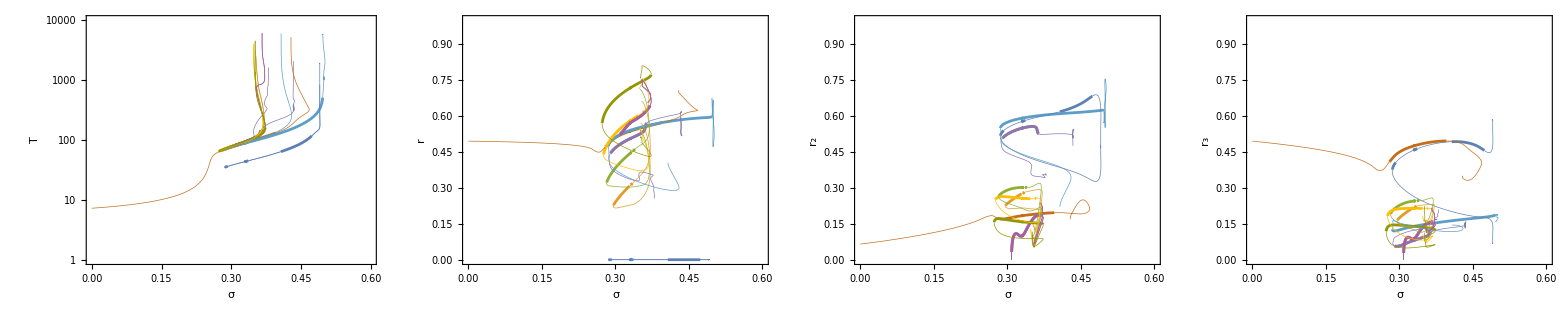

```mathematica
stable={};
unstable={};
M=10;
Do[
branch=Catenate[{Reverse[DeleteCases[Import["auto/janus/chimeras/"<>ToString[i]<>"rv.dat"],{}]],DeleteCases[Import["auto/janus/chimeras/"<>ToString[i]<>"fw.dat"],{}]}];
stables={};
unstables={};
part={};
stab=0;
Do[If[stab==0,If[branch[[i,7]]<4*M-2 , AppendTo[part,branch[[i]]];,stab=1;AppendTo[unstables,part];part={branch[[i]]};], If[branch[[i,7]]<4*M-2,stab=0;AppendTo[stables,part];part={branch[[i]]};,AppendTo[part,branch[[i]]];];];,{i,1,Length[branch]}];
If[stab==0,AppendTo[unstables,part],AppendTo[stables,part]];AppendTo[stable,stables];AppendTo[unstable,unstables];,{i,1,10}];

Grid[{{Show[Show[Table[ListLogPlot[stable[[i,All,All,{1,3}]],PlotRange->{{0,0.6},{1,10^4}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,T},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[i]]]],{i,1,10}]],Show[Table[ListLogPlot[unstable[[i,All,All,{1,3}]],PlotRange->{{0,0.6},{1,10^4}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,T},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5],ColorData[97,"ColorList"][[i]]]],{i,{1,2,3,5,6,7,8,9,10}}]]],Show[Show[Table[ListPlot[stable[[i,All,All,{1,4}]],PlotRange->{{0,0.6},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[i]]]],{i,1,10}]],Show[Table[ListPlot[unstable[[i,All,All,{1,4}]],PlotRange->{{0,0.6},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5],ColorData[97,"ColorList"][[i]]]],{i,{1,2,3,5,6,7,8,9,10}}]]],Show[Show[Table[ListPlot[stable[[i,All,All,{1,5}]],PlotRange->{{0,0.6},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,Subscript[r,2]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[i]]]],{i,1,10}]],Show[Table[ListPlot[unstable[[i,All,All,{1,5}]],PlotRange->{{0,0.6},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,Subscript[r,2]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5],ColorData[97,"ColorList"][[i]]]],{i,{1,2,3,5,6,7,8,9,10}}]]],Show[Show[Table[ListPlot[stable[[i,All,All,{1,6}]],PlotRange->{{0,0.6},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,Subscript[r,3]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[i]]]],{i,1,10}]],Show[Table[ListPlot[unstable[[i,All,All,{1,6}]],PlotRange->{{0,0.6},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,Subscript[r,3]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5],ColorData[97,"ColorList"][[i]]]],{i,{1,2,3,5,6,7,8,9,10}}]]]}}]
```

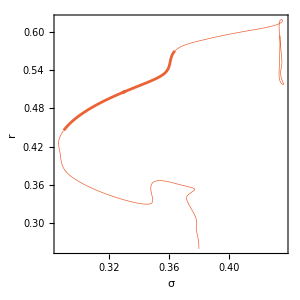

```mathematica
i=4;
Show[Show[ListPlot[stable[[i,All,All,{1,4}]],PlotRange->{{0,0.6},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[i]]]]],Show[ListPlot[unstable[[i,All,All,{1,4}]],PlotRange->{{0,0.6},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5],ColorData[97,"ColorList"][[i]]]]],PlotRange->Automatic]
```

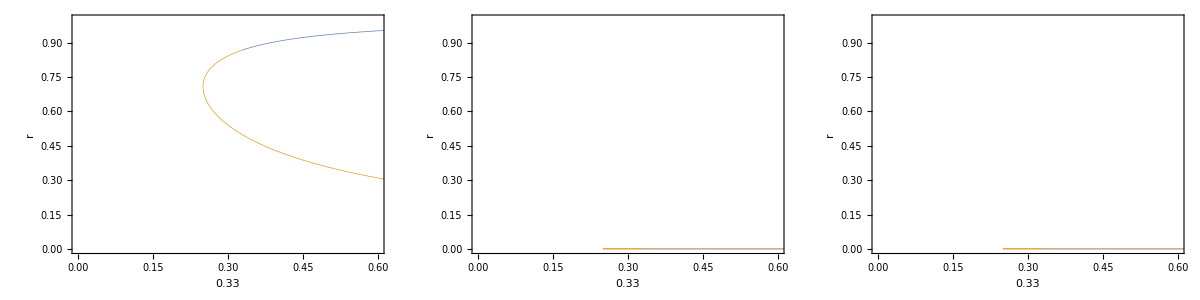

```mathematica
steady=Join[{#[[1;;Position[#,{}][[1,1]]-1]]},Table[#[[Position[#,{}][[i,1]]+1;;Position[#,{}][[i+1,1]]-1]],{i,1,Length[Position[#,{}]]-1}]]&@Import["auto/steady/steady.dat"];
Grid[{{ListPlot[steady[[All,All,{1,4}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]],ListPlot[steady[[All,All,{1,5}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]],ListPlot[steady[[All,All,{1,6}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]}}]
```

```mathematica
twists1=Join[{#[[1;;Position[#,{}][[1,1]]-1]]},Table[#[[Position[#,{}][[i,1]]+1;;Position[#,{}][[i+1,1]]-1]],{i,1,Length[Position[#,{}]]-1}]]&@Import["auto/twist1/twists.dat"];
Grid[{{rasterizeBackground[ListPlot[twists1[[All,All,{1,4}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]],rasterizeBackground[ListPlot[twists1[[All,All,{1,5}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]],rasterizeBackground[ListPlot[twists1[[All,All,{1,6}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]]}}]
```

-Graphics- | -Graphics- | -Graphics-

```mathematica
twists2=Join[{#[[1;;Position[#,{}][[1,1]]-1]]},Table[#[[Position[#,{}][[i,1]]+1;;Position[#,{}][[i+1,1]]-1]],{i,1,Length[Position[#,{}]]-1}]]&@Import["auto/twist2/twists.dat"];
Grid[{{rasterizeBackground[ListPlot[twists2[[All,All,{1,4}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]],rasterizeBackground[ListPlot[twists2[[All,All,{1,5}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]],rasterizeBackground[ListPlot[twists2[[All,All,{1,6}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]]}}]
```

-Graphics- | -Graphics- | -Graphics-

```mathematica
clusters1=Join[{#[[1;;Position[#,{}][[1,1]]-1]]},Table[#[[Position[#,{}][[i,1]]+1;;Position[#,{}][[i+1,1]]-1]],{i,1,Length[Position[#,{}]]-1}]]&@Import["auto/clusters1/clusters.dat"];
Grid[{{rasterizeBackground[ListPlot[clusters1[[All,All,{1,4}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]],rasterizeBackground[ListPlot[clusters1[[All,All,{1,5}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]],rasterizeBackground[ListPlot[clusters1[[All,All,{1,6}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]]}}]
```

-Graphics- | -Graphics- | -Graphics-

```mathematica
clusters2=Join[{#[[1;;Position[#,{}][[1,1]]-1]]},Table[#[[Position[#,{}][[i,1]]+1;;Position[#,{}][[i+1,1]]-1]],{i,1,Length[Position[#,{}]]-1}]]&@Import["auto/clusters2/clusters.dat"];
Grid[{{rasterizeBackground[ListPlot[clusters2[[All,All,{1,4}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]],rasterizeBackground[ListPlot[clusters2[[All,All,{1,5}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]],rasterizeBackground[ListPlot[clusters2[[All,All,{1,6}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]]}}]
```

-Graphics- | -Graphics- | -Graphics-

```mathematica
all=Join[steady,twists1,twists2,clusters1,clusters2];
Grid[{{rasterizeBackground[ListPlot[all[[All,All,{1,4}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]],rasterizeBackground[ListPlot[all[[All,All,{1,5}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]],rasterizeBackground[ListPlot[all[[All,All,{1,6}]],PlotRange->{{0,0.6},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]]}}]
```

-Graphics- | -Graphics- | -Graphics-

```mathematica
AbsoluteTiming[Monitor[branches=Table[Import["auto/clusters/branches/"<>ToString[i]<>".dat"],{i,1,6099}];,i]]
```

{523.051,Null}

```mathematica
dist[branch1_,branch2_]:=Module[{min,max,c1,c2,f1,f2,x,range},
{min,max}={Max[{Min[branch1[[All,1]]],Min[branch2[[All,1]]]}],Min[{Max[branch1[[All,1]]],Max[branch2[[All,1]]]}]};
c1=Cases[DeleteDuplicatesBy[branch1,#[[1]]&],u_/;u[[1]]>=min&&u[[1]]<=max];
c2=Cases[DeleteDuplicatesBy[branch2,#[[1]]&],u_/;u[[1]]>=min&&u[[1]]<=max];
{min,max}={Max[{Min[c1[[All,1]]],Min[c2[[All,1]]]}],Min[{Max[c1[[All,1]]],Max[c2[[All,1]]]}]};
If[max>min&&Length[c1]>1&&Length[c2]>1,f1=Interpolation[c1[[All,{1,4}]],InterpolationOrder->1];
f2=Interpolation[c2[[All,{1,4}]],InterpolationOrder->1];
range=(max-min);
Sum[Abs[f1[x]-f2[x]],{x,min+range/100,max-range/100,range/100}]/range,Infinity]]
AbsoluteTiming[Monitor[distances=Flatten[Table[{i,j,dist[branches[[i]],branches[[j]]]},{i,1,1},{j,i+1,Length[branches]}],1];,{i,j}]]
Cases[distances,u_/;u[[1]]<1]
```

{39.8638,Null}

{}

```mathematica
AbsoluteTiming[rasterizeBackground[ListPlot[branches[[1;;4000,All,{1,4}]],PlotRange->{{0,1},{0,1}},Joined->True,PlotRange->{{0,0.5},{0,1}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.5]]]]]
```

{112.404,-Graphics-}

### pendula

#### Single trajectory runs

```mathematica
filebase="data/test";
{M,t1,t0,dt,amp,omega}=Import[filebase<>"out.dat"][[2]]
dat=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];
Grid[{{rasterizeBackground[ListPlot[Transpose[{dt*Range[Length[dat]],Norm[#[[1;;M]]]&/@dat}],Axes->False,Frame->True,FrameLabel->{t,norm},LabelStyle->Directive[16,Black],FrameStyle->Directive[AbsoluteThickness[1],Black],AspectRatio->1,ImageSize->300]],rasterizeBackground[ListDensityPlot[dat[[-Round[50/dt];;-1;;Round[1/dt],1;;M+1]],InterpolationOrder->0,Frame->True,FrameLabel->{i,t},LabelStyle->Directive[16,Black],FrameStyle->Directive[AbsoluteThickness[1],Black],AspectRatio->1,ImageSize->300,ColorFunctionScaling->False,PlotRange->All,ColorFunction->cf]]}}]
```

{1000,10000.,9000.,0.05,0.058,3.35}

-Graphics- | -Graphics-

```mathematica
rasterizeBackground[ListDensityPlot[dat[[-Round[50/dt];;-1;;Round[1/dt],1;;M+1;;2]],InterpolationOrder->0,Frame->True,FrameLabel->{i,t},LabelStyle->Directive[16,Black],FrameStyle->Directive[AbsoluteThickness[1],Black],AspectRatio->1,ImageSize->300,ColorFunctionScaling->True,PlotRange->All]]
```

-Graphics-

```mathematica
rasterizeBackground[ListDensityPlot[Sqrt/@Mean/@Partition[dat[[All,1;;M+1]]^2,1*Round[1/dt]],InterpolationOrder->0,Frame->True,FrameLabel->{i,t},LabelStyle->Directive[16,Black],FrameStyle->Directive[AbsoluteThickness[1],Black],AspectRatio->1,ImageSize->300,PlotRange->All]]
```

-Graphics-

32

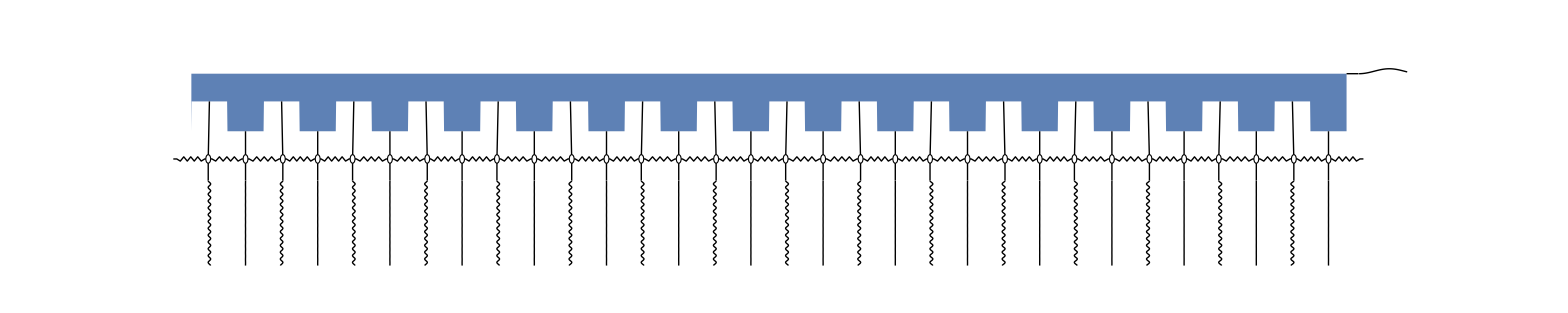

```mathematica
spring[p0_,p1_,divs_,height_]:=Module[{L,xhat,yhat},L=Norm[p1-p0]; xhat=(p1-p0)/L; yhat={xhat[[2]],-xhat[[1]]};Join[{p0,p0+L/divs*xhat},Table[p0+i*L/divs*xhat+height*yhat*(-1)^i,{i,2,divs-2}],{p1-L/divs*xhat,p1}]]

amax=amp;
ωd=1;
dx=1.5;
dn=500;
M=32
n1=Length[dat]-Round[2/dt];
n0=n1;
n=n1;
thetas=dat[[n,1;;M]];
thetas2=dat[[n-dn;;n,1;;M]];
lengths=Riffle[ConstantArray[0.35,M/2],ConstantArray[-0.35,M/2]];
f[x_]:=lengths[[1+Mod[Round[x/dx]-1,M]]];
z0={0,-amax*Cos[ωd*dt/ωd*(n-n0)]};
p0=Graphics[{ColorData[97,"ColorList"][[1]],Polygon[Join[{{dx/2,z0[[2]]+2}},Table[{x,z0[[2]]+1+f[x]},{x,dx*1/2,dx*(M+1/2),dx/100}],{{dx*(M+1/2),z0[[2]]+2},{dx/2,z0[[2]]+2}}]],Black,Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},{0,-1/2}+z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]}}],{i,1,M}],
Table[Line[Table[{0,-1/2}+z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas2[[dn+1-m,i]]],Cos[thetas2[[dn+1-m,i]]]}-{0,2/dn*m},{m,1,dn}]],{i,1,M}],

Line[{{dx*(M+1/2),z0[[2]]+2},{0.5+dx*(M+1/2),z0[[2]]+2}}],
Line[{0.5+dx*(M+1/2),2}+#&/@Transpose[{0.02*Range[101],Reverse[Table[-amax*Cos[ωd*dt/ωd*(m-n0)],{m,n-100,n,1}]]}]],

Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*(i+1),1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{dx*M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx*(M+1),1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],White,Table[Disk[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}]},ImageSize->2000,PlotRange->{-2+dx*{1/2,M+3.5+1/2},{-3,3}}]
```

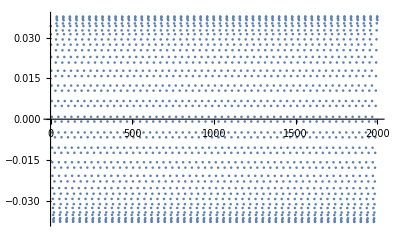

```mathematica
ListPlot[dat[[-2000;;-1,1]]]
```

#### AUTO limit cycle

```mathematica
M=16
filebase0="data/pendula/04"
{bins,counts}=HistogramList[Import[filebase0<>".dat"][[All,2]],{Table[i,{i,0,2.5,0.01}]}];
nonzero=First/@Position[counts,u_/;u>0];
sorted=Table[Cases[Import[filebase0<>".dat"],u_/;u[[2]]>bins[[j]]&&u[[2]]<bins[[j+1]]],{j,nonzero}];
{Length[Flatten[sorted,1]],Length[sorted]}
solitons=First/@sorted
```

16

data/pendula/04

{1022,32}

{{29,0.000128944},{9,1.43622},{157,1.79807},{3,1.83669},{25,1.85635},{18,1.86243},{27,1.94444},{89,1.97538},{32,2.03164},{98,2.04278},{28,2.05392},{10,2.06218},{6,2.10434},{2,2.11468},{45,2.12925},{49,2.13635},{14,2.14551},{5,2.21343},{150,2.23456},{17,2.24181},{48,2.25002},{99,2.26375},{173,2.27093},{651,2.28468},{16,2.3596},{161,2.36205},{112,2.37422},{1023,2.39875},{309,2.40959},{488,2.41823},{374,2.43399},{1000,2.45636}}

```mathematica
file=OpenWrite[filebase0<>"solitons.sh"];
WriteLine[file,"mkdir -p "<>filebase0];
Do[WriteLine[file,"./pendula.py --delta 0.4 --frequency 3.5 --amplitude 0.05 --init 0.5 --cycles 5000 --outcycle 4900 --dt 0.01 --num "<>ToString[M]<>" --seed "<>ToString[solitons[[i,1]]]<>" --filebase "<>filebase0<>"/soliton"<>ToString[i]],{i,1,Length[solitons]}]
Close[file]
```

data/pendula/04solitons.sh

```mathematica
ind=1;
If[!DirectoryQ[filebase0<>"/ics"],CreateDirectory[filebase0<>"/ics"]];

Grid[Table[filebase=filebase0<>"/soliton"<>ToString[i];
{M,t1,t0,dt,amp,omega}=Import[filebase<>"out.dat"][[2]];
dat=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];If[Mean[Differences[Norm[#[[1;;M]]]&/@dat[[1;;-1;;Round[2/dt]]]]^2]<10^-4,limit=Transpose[Catenate[{N[{2*Pi*dt*Range[0,2/dt]}],Transpose[Cos[dat[[1;;Round[2/dt]+1,1;;M;;2]]]],Transpose[Sin[dat[[1;;Round[2/dt]+1,1;;M;;2]]]],Transpose[dat[[1;;Round[2/dt]+1,M+1;;2*M;;2]]],Transpose[Cos[dat[[1;;Round[2/dt]+1,2;;M;;2]]]],Transpose[Sin[dat[[1;;Round[2/dt]+1,2;;M;;2]]]],Transpose[dat[[1;;Round[2/dt]+1,M+2;;2*M;;2]]],N[{Cos[2*Pi*dt*(Range[0,2/dt])],Sin[2*Pi*dt*(Range[0,2/dt])]}]}]];Export[filebase0<>"/ics"<>"/"<>ToString[ind]<>".dat",limit];
ind=ind+1;];
{rasterizeBackground[ListPlot[Transpose[{dt*Range[Length[dat]],Norm[#[[1;;M]]]&/@dat}],Axes->False,Frame->True,FrameLabel->{t,norm},LabelStyle->Directive[16,Black],FrameStyle->Directive[AbsoluteThickness[1],Black],AspectRatio->1,ImageSize->300]],rasterizeBackground[ListDensityPlot[dat[[-Round[50/dt];;-1;;Round[1/dt],1;;M+1]],InterpolationOrder->0,Frame->True,FrameLabel->{i,t},LabelStyle->Directive[16,Black],FrameStyle->Directive[AbsoluteThickness[1],Black],AspectRatio->1,ImageSize->300,ColorFunctionScaling->False,ColorFunction->cf]],Mean[Differences[Norm[#[[1;;M]]]&/@dat[[1;;-1;;Round[2/dt]]]]^2]<10^-4},{i,1,Length[solitons]}]]
```

-Graphics- | -Graphics- | True
-Graphics- | -Graphics- | True
-Graphics- | -Graphics- | True
-Graphics- | -Graphics- | True
-Graphics- | -Graphics- | True
-Graphics- | -Graphics- | True
-Graphics- | -Graphics- | True
-Graphics- | -Graphics- | True
-Graphics- | -Graphics- | False
-Graphics- | -Graphics- | False
-Graphics- | -Graphics- | False
-Graphics- | -Graphics- | False
-Graphics- | -Graphics- | False
-Graphics- | -Graphics- | False
-Graphics- | -Graphics- | False
-Graphics- | -Graphics- | False
-Graphics- | -Graphics- | False
-Graphics- | -Graphics- | True
-Graphics- | -Graphics- | True
-Graphics- | -Graphics- | True
-Graphics- | -Graphics- | True
-Graphics- | -Graphics- | True
-Graphics- | -Graphics- | True
-Graphics- | -Graphics- | False
-Graphics- | -Graphics- | False
-Graphics- | -Graphics- | False
-Graphics- | -Graphics- | False
-Graphics- | -Graphics- | True
-Graphics- | -Graphics- | False
-Graphics- | -Graphics- | False
-Graphics- | -Graphics- | False
-Graphics- | -Graphics- | True

#### Plots of sweeps

```mathematica
stable={};
unstable={};
branches={};
M=8;
filebase="auto/pendula/03_2/";
Do[
branch=DeleteCases[Import[file],{}];
AppendTo[branches,branch];
stables={};
unstables={};
part={};
stab=0;
Do[If[stab==0,If[branch[[i,4]]<6*M+2 , AppendTo[part,branch[[i]]];,stab=1;AppendTo[unstables,part];part={branch[[i]]};], If[branch[[i,4]]<6*M+2,stab=0;AppendTo[stables,part];part={branch[[i]]};,AppendTo[part,branch[[i]]];];];,{i,1,Length[branch]}];
If[stab==0,AppendTo[unstables,part],AppendTo[stables,part]];AppendTo[stable,Cases[stables,u_/;Length[u]>10]];AppendTo[unstable,unstables];,{file,FileNames[filebase<>"branches/*.dat"]}];
unstable=DeleteCases[#,{}]&/@unstable;
stable=DeleteCases[#,{}]&/@stable;
stable=DeleteCases[#,u_/;u[[1]]==0.05]&/@#&/@stable;

istable=First/@Position[Length/@stable,u_/;u>0];
iunstable=First/@Position[Length/@unstable,u_/;u>0];
p=Grid[{{Show[Show[Table[ListPlot[stable[[i,All,All,{1,5}]],PlotRange->{{0,0.5},{-1,Max[unstable[[All,All,All,5]]]}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,Subscript[r,1]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[2],CapForm["Round"],ColorData[97,"ColorList"][[Mod[i-1,15]+1]]]],{i,istable}]],Show[Table[ListPlot[branches[[i,All,{1,5}]],PlotRange->{{0,0.5},{-1,Max[unstable[[All,All,All,5]]]}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,Subscript[r,1]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.1],ColorData[97,"ColorList"][[Mod[i-1,15]+1]]]],{i,iunstable}]]],Show[Show[Table[ListPlot[stable[[i,All,All,{1,6}]],PlotRange->{{0,0.5},{-1,Max[unstable[[All,All,All,6]]]}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,Subscript[r,2]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[2],CapForm["Round"],ColorData[97,"ColorList"][[Mod[i-1,15]+1]]]],{i,istable}]],Show[Table[ListPlot[branches[[i,All,{1,6}]],PlotRange->{{0,0.5},{-1,Max[unstable[[All,All,All,6]]]}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,Subscript[r,2]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.1],ColorData[97,"ColorList"][[Mod[i-1,15]+1]]]],{i,iunstable}]]]}}];
Export[filebase<>"diagram.pdf",p]
p2=Grid[{{Show[Show[Table[ListPlot[stable[[i,All,All,{1,5}]],PlotRange->{{0,0.1},{-1,Max[unstable[[All,All,All,5]]]}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,Subscript[r,1]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[2],CapForm["Round"],ColorData[97,"ColorList"][[Mod[i-1,15]+1]]]],{i,istable}]],Show[Table[ListPlot[branches[[i,All,{1,5}]],PlotRange->{{0,0.1},{-1,Max[unstable[[All,All,All,5]]]}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,Subscript[r,1]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.1],ColorData[97,"ColorList"][[Mod[i-1,15]+1]]]],{i,iunstable}]]],Show[Show[Table[ListPlot[stable[[i,All,All,{1,6}]],PlotRange->{{0,0.1},{-1,Max[unstable[[All,All,All,6]]]}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,Subscript[r,2]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[2],CapForm["Round"],ColorData[97,"ColorList"][[Mod[i-1,15]+1]]]],{i,istable}]],Show[Table[ListPlot[branches[[i,All,{1,6}]],PlotRange->{{0,0.1},{-1,Max[unstable[[All,All,All,6]]]}},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,Subscript[r,2]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotStyle->Directive[AbsoluteThickness[0.1],ColorData[97,"ColorList"][[Mod[i-1,15]+1]]]],{i,iunstable}]]]}}];
Export[filebase<>"diagram2.pdf",p2]
```

auto/pendula/03_2/diagram.pdf

auto/pendula/03_2/diagram2.pdf